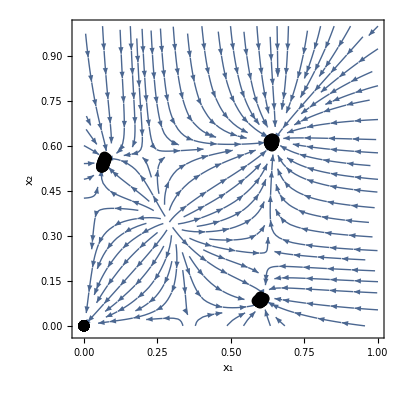

```mathematica
k=20;
q=20;
Subscript[ϵ, 2]=0.5;
Subscript[ϵ, 3]=0.95;
ρ=0.506;
γ=1;
Subscript[β, 2]=0.2/k;
Subscript[β, 3]=4/q;
Subscript[r, 2]=(1-ρ^2-(1-ρ)^2)/(ρ^2+(1-ρ)^2);
Subscript[r, 3]=(1-ρ^3-(1-ρ)^3)/(ρ^3+(1-ρ)^3);
data = Import["/Users/nicholaslandry/Documents/GitHub/polarizability-in-hypergraphs/Data/polarization/0.506-0.5-0.95.json"];
pts = "fixed-points"/. data;
Show[StreamPlot[{-γ Subscript[x, 1]+Subscript[β, 2] k(1-Subscript[x, 1])(ρ(1+Subscript[r, 2] Subscript[ϵ, 2])Subscript[x, 1]+(1-ρ)(1-Subscript[ϵ, 2])Subscript[x, 2])+Subscript[β, 3] q(1-Subscript[x, 1])(ρ^2(1+Subscript[r, 3] Subscript[ϵ, 3])Subscript[x, 1]^2+2(1-ρ)ρ(1-Subscript[ϵ, 3])Subscript[x, 1] Subscript[x, 2]+(1-ρ)^2(1-Subscript[ϵ, 3])Subscript[x, 2]^2),-γ Subscript[x, 2]+Subscript[β, 2] k(1-Subscript[x, 2])((1-ρ)(1+Subscript[r, 2] Subscript[ϵ, 2])Subscript[x, 2]+ρ(1-Subscript[ϵ, 2])Subscript[x, 1])+Subscript[β, 3] q(1-Subscript[x, 2])((1-ρ)^2(1+Subscript[r, 3] Subscript[ϵ, 3])Subscript[x, 2]^2+2(1-ρ)ρ(1-Subscript[ϵ, 3])Subscript[x, 2] Subscript[x, 1]+ρ^2(1-Subscript[ϵ, 3])Subscript[x, 1]^2)},{Subscript[x, 1],0,1},{Subscript[x, 2],0,1},Axes->True,FrameLabel->{"x_1","x_2"},LabelStyle->Directive[Black,Bold,24], PlotRange->{{-0.02,1},{-0.02,1}},StreamColorFunction->None],ListPlot[pts,PlotStyle->Directive[Black,PointSize[.02]]]]
```

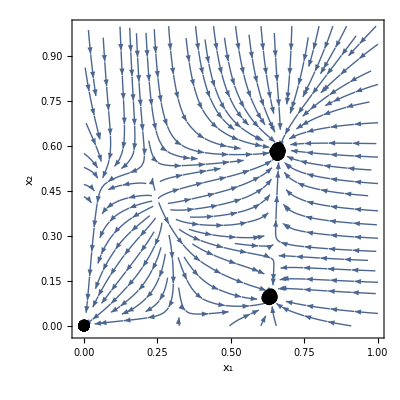

```mathematica
k=20;
q=20;
Subscript[ϵ, 2]=0.5;
Subscript[ϵ, 3]=0.95;
ρ=0.515;
γ=1;
Subscript[β, 2]=0.2/k;
Subscript[β, 3]=4/q;
Subscript[r, 2]=(1-ρ^2-(1-ρ)^2)/(ρ^2+(1-ρ)^2);
Subscript[r, 3]=(1-ρ^3-(1-ρ)^3)/(ρ^3+(1-ρ)^3);
data = Import["/Users/nicholaslandry/Documents/GitHub/polarizability-in-hypergraphs/Data/polarization/0.515-0.5-0.95.json"];
pts = "fixed-points"/. data;
Show[StreamPlot[{-γ Subscript[x, 1]+Subscript[β, 2] k(1-Subscript[x, 1])(ρ(1+Subscript[r, 2] Subscript[ϵ, 2])Subscript[x, 1]+(1-ρ)(1-Subscript[ϵ, 2])Subscript[x, 2])+Subscript[β, 3] q(1-Subscript[x, 1])(ρ^2(1+Subscript[r, 3] Subscript[ϵ, 3])Subscript[x, 1]^2+2(1-ρ)ρ(1-Subscript[ϵ, 3])Subscript[x, 1] Subscript[x, 2]+(1-ρ)^2(1-Subscript[ϵ, 3])Subscript[x, 2]^2),-γ Subscript[x, 2]+Subscript[β, 2] k(1-Subscript[x, 2])((1-ρ)(1+Subscript[r, 2] Subscript[ϵ, 2])Subscript[x, 2]+ρ(1-Subscript[ϵ, 2])Subscript[x, 1])+Subscript[β, 3] q(1-Subscript[x, 2])((1-ρ)^2(1+Subscript[r, 3] Subscript[ϵ, 3])Subscript[x, 2]^2+2(1-ρ)ρ(1-Subscript[ϵ, 3])Subscript[x, 2] Subscript[x, 1]+ρ^2(1-Subscript[ϵ, 3])Subscript[x, 1]^2)},{Subscript[x, 1],0,1},{Subscript[x, 2],0,1},Axes->True,FrameLabel->{"x_1","x_2"},LabelStyle->Directive[Black,Bold,24], PlotRange->{{-0.02,1},{-0.02,1}},StreamColorFunction->None],ListPlot[pts,PlotStyle->Directive[Black,PointSize[.02]]]]
```

```mathematica
k=20;
q=20;
Subscript[ϵ, 2]=0.18;
Subscript[ϵ, 3]=0.95;
ρ=0.506;
γ=1;
Subscript[β, 2]=0.2/k;
Subscript[β, 3]=4/q;
Subscript[r, 2]=(1-ρ^2-(1-ρ)^2)/(ρ^2+(1-ρ)^2);
Subscript[r, 3]=(1-ρ^3-(1-ρ)^3)/(ρ^3+(1-ρ)^3);
data = Import["/Users/nicholaslandry/Documents/GitHub/polarizability-in-hypergraphs/Data/polarization/0.506-0.18-0.95.json"];
pts = "fixed-points"/. data;
data = Import["/Users/nicholaslandry/Documents/GitHub/polarizability-in-hypergraphs/Data/polarization/0.506-0.18-0.95-trajectories.json"];
x0 = "0-x"/.data;
x1 = "1-x"/.data;
x2 = "2-x"/.data;
x3 = "3-x"/.data;
x4 = "4-x"/.data;
```

```mathematica
t = 0.0025;
trajectorycolor = Black;
a =0.5;
Show[StreamPlot[{-γ Subscript[x, 1]+Subscript[β, 2] k(1-Subscript[x, 1])(ρ(1+Subscript[r, 2] Subscript[ϵ, 2])Subscript[x, 1]+(1-ρ)(1-Subscript[ϵ, 2])Subscript[x, 2])+Subscript[β, 3] q(1-Subscript[x, 1])(ρ^2(1+Subscript[r, 3] Subscript[ϵ, 3])Subscript[x, 1]^2+2(1-ρ)ρ(1-Subscript[ϵ, 3])Subscript[x, 1] Subscript[x, 2]+(1-ρ)^2(1-Subscript[ϵ, 3])Subscript[x, 2]^2),
-γ Subscript[x, 2]+Subscript[β, 2] k(1-Subscript[x, 2])((1-ρ)(1+Subscript[r, 2] Subscript[ϵ, 2])Subscript[x, 2]+ρ(1-Subscript[ϵ, 2])Subscript[x, 1])+Subscript[β, 3] q(1-Subscript[x, 2])((1-ρ)^2(1+Subscript[r, 3] Subscript[ϵ, 3])Subscript[x, 2]^2+2(1-ρ)ρ(1-Subscript[ϵ, 3])Subscript[x, 2] Subscript[x, 1]+ρ^2(1-Subscript[ϵ, 3])Subscript[x, 1]^2)},{Subscript[x, 1],0,1},{Subscript[x, 2],0,1},Axes->True,FrameLabel->{"x_1","x_2"},LabelStyle->Directive[Black,Bold,24], PlotRange->{{-0.02,1},{-0.02,1}},StreamColorFunction->None],ListLinePlot[x0,PlotStyle->Directive[Lighter[trajectorycolor, 0], Thickness[t], Opacity[a]], PlotRange->Full],ListLinePlot[x1,PlotStyle->Directive[Lighter[trajectorycolor, 0.2], Thickness[t], Opacity[a]], PlotRange->Full],ListLinePlot[x2,PlotStyle->Directive[Lighter[trajectorycolor, 0.4], Thickness[t], Opacity[a]], PlotRange->Full],ListLinePlot[x3,PlotStyle->Directive[Lighter[trajectorycolor, 0.6], Thickness[t], Opacity[a]], PlotRange->Full],ListLinePlot[x4,PlotStyle->Directive[Lighter[trajectorycolor, 0.8], Thickness[t], Opacity[a]], PlotRange->Full],ListPlot[pts,PlotStyle->Directive[Black,PointSize[.02]]]]
```

-Graphics-

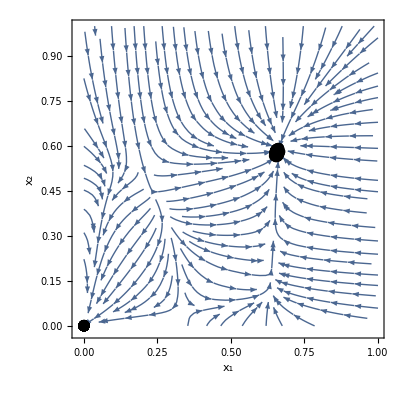

```mathematica
k=20;
q=20;
Subscript[ϵ, 2]=0.18;
Subscript[ϵ, 3]=0.95;
ρ=0.515;
γ=1;
Subscript[β, 2]=0.2/k;
Subscript[β, 3]=4/q;
Subscript[r, 2]=(1-ρ^2-(1-ρ)^2)/(ρ^2+(1-ρ)^2);
Subscript[r, 3]=(1-ρ^3-(1-ρ)^3)/(ρ^3+(1-ρ)^3);
data = Import["/Users/nicholaslandry/Documents/GitHub/polarizability-in-hypergraphs/Data/polarization/0.515-0.18-0.95.json"];
pts = "fixed-points"/. data;
Show[StreamPlot[{-γ Subscript[x, 1]+Subscript[β, 2] k(1-Subscript[x, 1])(ρ(1+Subscript[r, 2] Subscript[ϵ, 2])Subscript[x, 1]+(1-ρ)(1-Subscript[ϵ, 2])Subscript[x, 2])+Subscript[β, 3] q(1-Subscript[x, 1])(ρ^2(1+Subscript[r, 3] Subscript[ϵ, 3])Subscript[x, 1]^2+2(1-ρ)ρ(1-Subscript[ϵ, 3])Subscript[x, 1] Subscript[x, 2]+(1-ρ)^2(1-Subscript[ϵ, 3])Subscript[x, 2]^2),-γ Subscript[x, 2]+Subscript[β, 2] k(1-Subscript[x, 2])((1-ρ)(1+Subscript[r, 2] Subscript[ϵ, 2])Subscript[x, 2]+ρ(1-Subscript[ϵ, 2])Subscript[x, 1])+Subscript[β, 3] q(1-Subscript[x, 2])((1-ρ)^2(1+Subscript[r, 3] Subscript[ϵ, 3])Subscript[x, 2]^2+2(1-ρ)ρ(1-Subscript[ϵ, 3])Subscript[x, 2] Subscript[x, 1]+ρ^2(1-Subscript[ϵ, 3])Subscript[x, 1]^2)},{Subscript[x, 1],0,1},{Subscript[x, 2],0,1},Axes->True,FrameLabel->{"x_1","x_2"},LabelStyle->Directive[Black,Bold,24], PlotRange->{{-0.02,1},{-0.02,1}},StreamColorFunction->None],ListPlot[pts,PlotStyle->Directive[Black,PointSize[.02]]]]
```